```mathematica
Pollination Mutualism Model
```

Author: Kayla R. S. Hale	Last Revised: Dec. 15, 2021

Cite this work as: 
Hale, K.R.S., Maes, D.P., & Valdovinos, F.S. (2021). Simple mechanisms of plant reproductive benefits yield different dynamics in pollination and seed dispersal mutualisms (in review).

Mutualism between animal seed dispersers which benefit plants by increasing the fraction of flowers that are pollinated () and plants which benefit animals by providing nutritional rewards. Plant () and animal seed disperser () population densities change over time according to the coupled differential equations:


where , and all other parameters must be positive. See Table 1 of Hale et al. 2021 (in review) for parameter definitions. 

Plants are obligate when   or facultative otherwise.
Animals are obligate when  or facultative otherwise.

Below, we create phase planes diagram to illustrate the unique, feasible dynamics for every combination of facultative or obligate plants paired with facultative or obligate animal dispersers.  The first code chunk provides comments to explain the formatting commands. Code chunks can be run independent of each other.

Obligate Plants, Obligate Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{-5.,0}

{0,-3.33333}

{{P→3.17157,A→6.2306},{P→1.25,A→3.33333}}

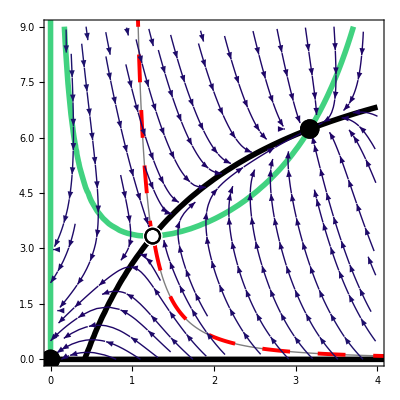

```mathematica
(* Obligate Plants, Obligate Animals *) 
Print["Obligate Plants, Obligate Animals" ]

(* Model Parameters *)
bP=1; f = 0.5; φ=0.5; g=1;sP=0.05; dP=0.75; 
a=0.8;h=1;
bA=1; ε=2; sA=0.15; dA=1.5;

(* Formatting Parameters *)
(* phase plane will be evaluated from min to max *) 
minP=0;minA=0; 
maxP=4;maxA=9;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(* Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues. *)
(* P: x-axis *)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
(* A: y-axis *)
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
(* creates vector field in a "stream" format with auto-sized vectors *)
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
(* curves in which the differential equation is 0 (no change in population density) *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
(* trivial nullclines in the sense that the change in population density is zero because the population density is zero *)
zeroP=Line[{{0,minA},{0,maxA+1}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP+1,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
(* equation for plant-only equilibrium (i.e., when animals are extinct) *)
plantonlyeq = {(bP*f*g-dP)/sP,0} ;
(* formats the point color and outline, which will be layered on top of each other in the final pahse plane *)
(* "preplantonlypt" used to set the color of the point: use white for saddle points, black for stable points, and red for unstable points *) 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Red, PointSize[pointSize]}];
(* "plantonlypt" draws the black outline image for the point regardless of color *)
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Red, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{Black,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names & colors for unstable and stable equilbiria. *)
(* coexistence equilibria are where the nontrivial nullclines are both equal to zero but both species densities are > 0 *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

(* first coexistence equilibrium *)
coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
(* formats the point color ("precoexistpt1") and outline ("coexistpt1") *)
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(* Finds the separatrices numerically. Using the full model avoids numerical plotting issues. *)
(* the separatrix is a curve that run through a saddle point to separate basins of attraction on either side *)
FP[P_,A_]=P*(bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
(* calculate a numerical solution to the differential equations *)
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}];

(* calculate the solution trajectory through the saddle point *) 
(* uses a parametric plotting function, to evaluate the trajectory forward in time from an initial point (the saddle point). sepxylim etc determines "how long" to evaluate the trajectory for. Adjust these values if there are numerical issues, like the trajectory isn't plotting, the trajectory isn't long enough for the window, etc. *)
(* separatrix is formatted as a thick dashed red line *) 
sepxylim=15;sepyxlim=8;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* plot the separatrices again with a thin gray line to make it easier to shade manually in Adobe Ilustrator by encloing a region of the phase space [purely for formatting] *)  
(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

(* Show all the graphics items layered on top of each other to create the phase plane *) 
(* asymptotes are excluded for publication-quality images; plot is padded so the extinction equilibruim is visible *)
Show[cpP, cpA,sepformxy,sepyformyx, trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Obligate Plants, Facultative Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{-5.,0}

{0,2.}

{{P→3.02367,A→6.29773},{P→0.826863,A→4.21069}}

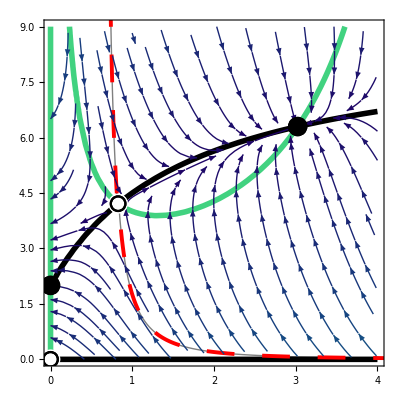

```mathematica
(* Obligate Plants, Facultative Animals *) 
Print["Obligate Plants, Facultative Animals" ]

bP=1; f = 0.5; φ=0.5; g=1;sP=0.05; dP=0.75; 
a=0.6;h=1;
bA=1; ε=1; sA=0.15; dA=0.7;

minP = 0; minA =0;
maxP=4;maxA=9;
plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0};
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Red, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Black, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(* Finds the separatrices numerically. Using the full model avoids numerical plotting issues. *)
FP[P_,A_]=P*(bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}];

sepxylim=16;sepyxlim=7;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,sepformxy,sepyformyx, trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Obligate Plants, Facultative Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{-1.06667,0}

{0,2.}

{{P→1.72912,A→6.65293},{P→0.717257,A→4.42538}}

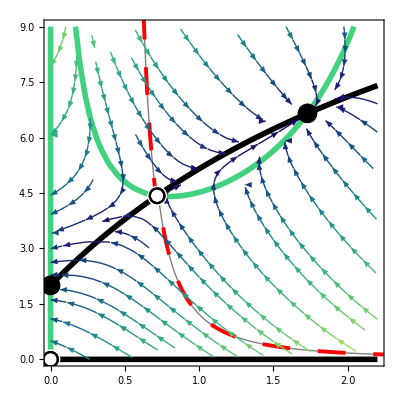

```mathematica
Print["Obligate Plants, Facultative Animals" ]

bP=1.2; f = 0.5; φ=0.5; g=1;sP=0.15; dP=0.76; 
a=0.31;h=1;
bA=1; ε=2; sA=0.15; dA=0.7;

minP = 0; minA =0;
maxP=2.2;maxA=9;
plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} ;
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Red, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Black, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria. *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(* Finds the separatrices numerically. Using the full model avoids numerical plotting issues. *)
FP[P_,A_]=P*(bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}];

sepxylim=13;sepyxlim=6;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,sepformxy,sepyformyx, trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Obligate Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{2.,0}

{0,-3.33333}

{{P→4.8412,A→7.26381}}

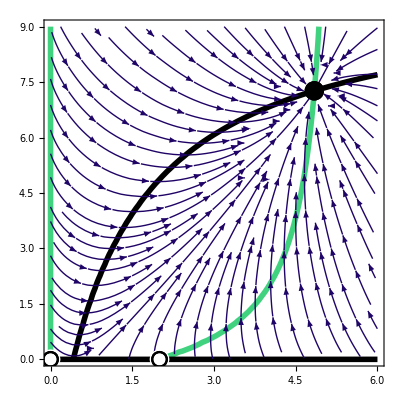

```mathematica
(* Facultative Plants, Obligate Animals *) 
Print["Facultative Plants, Obligate Animals" ]

bP=1; f = 0.5; φ=0.5; g=1;sP=0.15; dP=0.2; 
a=0.8;h=1;
bA=1; ε=2; sA=0.15; dA=1.5;
minP = 0; minA =0;
maxP=6;maxA=9;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0};
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{White, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Red, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria. *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,trivialP,trivialA, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Obligate Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{0.666667,0}

{0,-9.09091}

{{P→2.92421,A→3.12368},{P→1.72255,A→0.848129}}

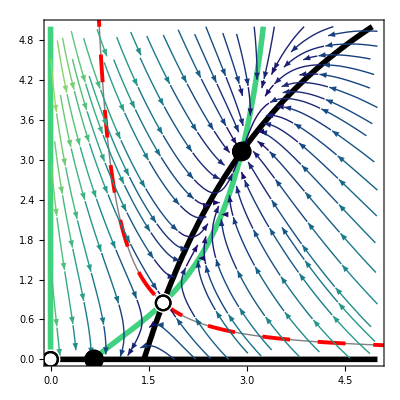

```mathematica
(* Facultative Plants, Obligate Animals *) 
Print["Facultative Plants, Obligate Animals" ]

(*bP=1; f = 0.5; φ=0.5; g=1;sP=0.14; dP=0.4; 
a=0.9;h=1;
bA=1; ε=2; sA=0.115; dA=2.1;
minP = 0; minA =0;
maxP=5;maxA=5;*)

bP=1; f = 0.5; φ=0.5; g=1;sP=.15; dP=0.4; 
a=0.7;h=1;
bA=1; ε=2; sA=0.11; dA=2.;
minP = 0; minA =0;
maxP=5;maxA=5;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} ;
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Black, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Red, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria. *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(* Finds the separatrices numerically. Using the full model avoids numerical plotting issues. *)
FP[P_,A_]=P*(bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}];

sepxylim=14;sepyxlim=14;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,sepformxy,sepyformyx, trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Obligate Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{0.131148,0}

{0,-0.05}

{{P→0.758418,A→0.697086},{P→0.431465,A→0.377774},{P→0.20055,A→0.149749}}

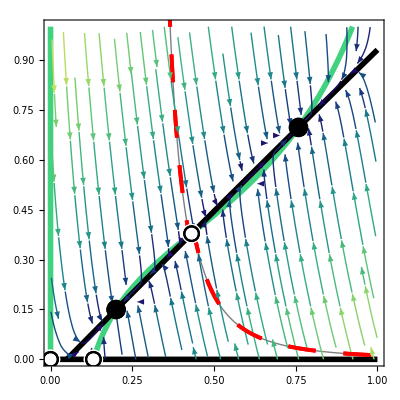

```mathematica
(* Facultative Plants, Obligate Animals *) 
Print["Facultative Plants, Obligate Animals" ]

bP=1.5; f = 0.5; φ=0.5; g=1;sP=0.61; dP=0.67; 
a=2.0;h=0.01;
bA=1; ε=1; sA=2; dA=1.1;

minP = 0;minA =0;
maxP=1;maxA=1;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} ;
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{White, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Red, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria. *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist3={P/.equilibria[[3]],A/.equilibria[[3]]}; 
precoexistpt3=ListPlot[{coexist3},PlotStyle->{Black, PointSize[0.035]}];
coexistpt3=ListPlot[{coexist3},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(* Finds the separatrices numerically. Using the full model avoids numerical plotting issues. *)
FP[P_,A_]=P*(bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}];

sepxylim=5.9;sepyxlim=3.5;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,sepformxy,sepyformyx,trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, sepxy2,sepyx2,precoexistpt3,coexistpt3,precoexistpt2,coexistpt2,precoexistpt1, coexistpt1,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Facultative Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{0.0833333,0}

{0,0.05}

{{P→0.700721,A→0.723994},{P→0.40724,A→0.443931},{P→0.153413,A→0.199132}}

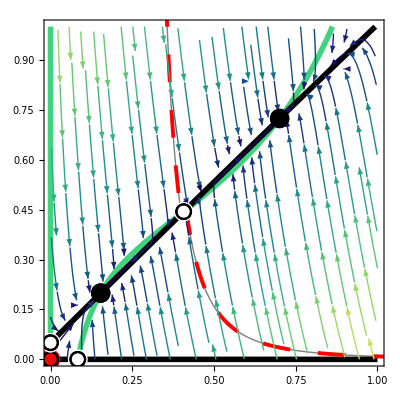

```mathematica
(* Facultative Plants, Facultative Animals *) 
Print["Facultative Plants, Facultative Animals" ]

bP=1.5; f = 0.5; φ=0.5; g=1;sP=0.6; dP=0.7; 
a=1.95;h=0.01;
bA=1; ε=1; sA=2; dA=0.9;

minP = 0; minA =0;
maxP=1;maxA=1;
plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0};
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{White, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{White, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{Red,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria. *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist3={P/.equilibria[[3]],A/.equilibria[[3]]}; 
precoexistpt3=ListPlot[{coexist3},PlotStyle->{Black, PointSize[0.035]}];
coexistpt3=ListPlot[{coexist3},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(* Finds the separatrices numerically. Using the full model avoids numerical plotting issues. *)
FP[P_,A_]=P*(bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}];

sepxylim=7;sepyxlim=3;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,sepformxy,sepyformyx, trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,precoexistpt3,coexistpt3,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Facultative Animals

Equilibria: (only non-negative values are relevant)

{0,0}

{2.,0}

{0,2.}

{{P→4.84326,A→7.29903}}

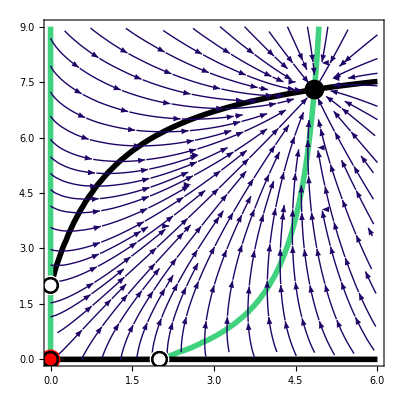

```mathematica
(* Facultative Plants, Facultative Animals *) 
Print["Facultative Plants, Facultative Animals" ]

bP=1; f = 0.5; φ=0.5; g=1;sP=0.15; dP=0.2; 
a=0.8;h=1;
bA=1; ε=1; sA=0.15; dA=0.7;

minP = 0; minA =0;
maxP=6;maxA=9;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(* Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues. *)
nP[P_,A_]=bP(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0};
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{White, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA};
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{White, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{Red,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(* Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria. *)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* print the equilbrium values for reference *)
Print["Equilibria: (only non-negative values are relevant)" ]
trivialeq
plantonlyeq
animalonlyeq
equilibria 

Show[cpP, cpA,trivialP,trivialA, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```